```mathematica
Pane[Grid[{
{Style["Fitting of a kinetic Host:Dye interaction","Chapter"]},
{MouseAppearance[Button[Style["Launch Application","Section"],{ nb=EvaluationNotebook[],NotebookFind[nb,"loadcellHD",All,CellTags],SelectionEvaluate[nb]},Appearance->None],"LinkHand"]}

}, Alignment->Center,ItemSize->Large,BaselinePosition->Baseline],Alignment->Center,ImageSize->Full]
```

Fitting of a kinetic Host:Dye interaction
Launch Application

```mathematica
(* Notebook settings
*)
SetOptions[EvaluationNotebook[],CellContext->Notebook];
SetOptions[$FrontEnd,GlobalInitializationCellWarning->False]
SetOptions[EvaluationNotebook[],CellEpilog:>SelectionMove[EvaluationNotebook[],All,EvaluationCell]]
SetOptions[EvaluationNotebook[],InitializationCellEvaluation->True,InitializationCellWarning->False]
SetOptions[$FrontEnd,"DynamicUpdating"->True];
SetOptions[$FrontEnd,"DynamicEvaluationTimeout"->30];

ClearAll[start,end,step,h0,h0in,h0error,h0fixed,d0,d0in,d0error,d0fixed,d0out,g0,g0in,g0error,g0fixed,kequhd,kequhdin,kequhderror,kequhdfixed,kequhdout,kequhdpos,kequhg,kequhgin,kequhgerror,kequhgfixed,kequhgout,kequhgpos,khd1,khd1in,khd2in,khd1error,khd1fixed,khd1out,khd1pos,khg1,khg1in,khg2in,khg1error,khg1fixed,khg1out,khg1pos,kg,kgin,kgerror,kgfixed,sig0,sig0in,sig0error,sig0fixed,sig0out,sighd,sighdin,sighderror,sighderror,sighdout,sigd,sigdin,sigderror,sigdfixed,sigdout,dataimport,bestfit,data,sig,datad,datahd,dataimport,datasignal,modelsignal,fit,fitplot,fitsignal,fitteddata,inputparameter,subparameter,concparameter,output,equns,equnsignal,solhd,sold,initials];
(* Load Packges*)	
	Get[FileNameJoin[{FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Packages","kinHD","kinHD2.m"}]}]];
	Get[FileNameJoin[{FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Packages","datagen.m"}]}]];
	Get[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Styles","styles.m"}]];
	
pathkinHD=FileNameJoin[{NotebookDirectory[],"Samples","kinHD-sim.txt"}];
savePath=FileNameJoin[{NotebookDirectory[],"Parameter","temp-kinHG.mx"}];

(* Paths*)
tempPath=FileNameJoin[{NotebookDirectory[],"Parameter","temp-kinHG.mx"}];
cachePath=FileNameJoin[{NotebookDirectory[],"Parameter","cache-kin.mx"}];
defaultPath=FileNameJoin[{NotebookDirectory[],"Parameter","default-kinHG.mx"}];
pathHG=FileNameJoin[{NotebookDirectory[],"Samples","Sim-kinHG.txt"}];
initialparameters={};
(*Buttons*)
initializebutton=MouseAppearance[Button[stylesButtonGenericStyle["Initialize","Initilize the values"],{ nb=EvaluationNotebook[],NotebookFind[nb,"initialroutineHD",All,CellTags],SelectionEvaluate[nb]},Appearance->None],"LinkHand"];
fitbutton=MouseAppearance[Button[stylesButtonGenericStyle["Click here to fit","Fits the model to the data"],{ nb=EvaluationNotebook[],NotebookFind[nb,"fixinitials",All,CellTags],SelectionEvaluate[nb],kb=EvaluationNotebook[],NotebookFind[kb,"fittingroutineHD",All,CellTags],SelectionEvaluate[kb]},Appearance->None],"LinkHand"];

variablessavebutton=MouseAppearance[Button[stylesButtonGenericStyle["Save Parameters","Saves the set values of the parameters"],{
initialparameters={
h0in,d0in,ga0in,
tmax,stepsize,
kequhdin,kequhddin,kequhgain,
khd1in,khdd1in,khga1in},Export[savePath,initialparameters]},Appearance->None],"LinkHand"];
variablesloadbutton=MouseAppearance[Button[stylesButtonGenericStyle["Load Saved Parameters","Loads the previously saved values"],{initialparameters=Import[savePath],
	h0in=initialparameters[[1]],
	d0in=initialparameters[[2]],
	ga0in=initialparameters[[3]],
	tmax=initialparameters[[4]],
	stepsize=initialparameters[[5]],
	kequhdin=initialparameters[[6]],
	kequhddin=initialparameters[[7]],
	kequhgain=initialparameters[[8]],
	khd1in=initialparameters[[9]],
	khdd1in=initialparameters[[10]],
	khga1in=initialparameters[[11]]
	},Appearance->None],"LinkHand"];

tmin=0;
tmax=10;
stepsize=tmax/100.;

QYhd=0.043;
QYhdd=0.023;
QYrin=QYhdd/QYhd;
h0in=3.2*10^-6;
ga0in=4.9*10^-6;
gb0in=5.9*10^-6;
d0in=10.*10^-6;
hga0in=0;
hd0in=0;

khga1in=1.8*10^7;
khgb1in=1.7*10^7;
khd1in=64.*10^6;
khdd1in=5.0*10^7;

kequhgain=7.82*^7;
kequhgbin=2.42*^7;
kequhdin=9.5*10^6;
kequhddin=2.2*10^6;

khga2in =khga1in/kequhgain;
khgb2in =khgb1in/kequhgbin;
khd2in =khd1in/kequhdin;
khdd2in=khdd1in/kequhddin;

khga1guess=1.*10^7;
khga2guess=0.9;
khd1guess=1;
khd2guess=0.9;

psguess=2;
gsguess=0.0;
psguess=0.1;

kequhgaerror=0;
kequhgberror=0;
khga1error=0;
khga2error=0;
start = 0.;

sighdin = 1.; 
sigdin = 0.; 
sig0in =  0.;
sighderror = 0;
sigderror = 0;
sig0error=0;
d0error=0;
h0error=0;
ga0error=0;

kequhderror=0;
kequhdderror=0;
kequhgaerror=0;
khga1error=0;
khga2error=0;
khd1error=0;
khd2error=0;
khdd1error=0;
khdd2error=0;

(*Parameter fixation*)
sighdfixed=2;
sigdfixed=2;
sig0fixed=2;

h0fixed=1;
ga0fixed=1;
d0fixed=1;

kequhdfixed=1;
kequhddfixed=1;
khd1fixed=1;
khdd1fixed=1;
khd2fixed=1;
kequhgafixed=1;
kequhgbfixed=1;
QYrfixed=1;
khga1fixed=2;
khga2fixed=1;
khgb1fixed=2;
khgb2fixed=1;

inputline1 = {
   {
   	Style["species", Bold,Underlined, FontSize->12 ,TextAlignment->Right], 
   	Style["concentration", Bold,Underlined, FontSize->12 ,TextAlignment->Right],"",
   	Style["binding", Bold,Underlined, FontSize->12 ,TextAlignment->Right],"","",
   	Style["association", Bold,Underlined, FontSize->12 ,TextAlignment->Right],"","",	Style["dissociation", Bold,Underlined, FontSize->12 ,TextAlignment->Right]},

   {
  	Style["Host:", Bold, FontSize->16 ,TextAlignment->Right], InputField[Dynamic[h0in], FieldSize -> 8],"M",
	Style["time-max = ", Bold, FontSize->16 ,TextAlignment->Right], InputField[Dynamic[tmax], FieldSize -> 8],"sec",Style["time-step = ", Bold, FontSize->16 ,TextAlignment->Right], InputField[Dynamic[stepsize], FieldSize -> 8],"sec"
},
 {"",Dynamic[h0in*1000000],"μM","end time","","","","","",""},
 
   {
   	Style["Dye:", Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[d0in], FieldSize -> 8],"M",Style["K_equ(HD)" , Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[kequhdin], FieldSize -> 8],"\!\(\*SuperscriptBox[\(M\), \(-1\)]\)",Style["k_1(HD)" , Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[khd1in], FieldSize -> 8],"\!\(\*SuperscriptBox[\(M\), \(-1\)]\) \!\(\*SuperscriptBox[\(s\), \(-1\)]\)",
	Style["k_-1(HD)" , Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[khd2in=khd1in/kequhdin,None], FieldSize -> 8,Background->LightGray],"\!\(\*SuperscriptBox[\(s\), \(-1\)]\)"
},

   {"",Dynamic[d0in*1000000],"μM","lg(K_equ)",Dynamic[Log10[kequhdin]],"","ingression","","","egression"},
   
     
   
   {Style["Signal-HD", Bold, FontSize->16 ,TextAlignment->Right], InputField[Dynamic[sighdin], FieldSize -> 8],"",
      Style["Signal-D", Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[sigdin], FieldSize -> 8],"",
   Style["Signal-0", Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[sig0in], FieldSize -> 8]},
      {"HD complex","","","dye alone","","","Startsignal"}  ,
    {Style["Show: ", Bold, FontSize->16 ,TextAlignment->Right],CheckboxBar[Dynamic[species],{1-> "Simulated signal",2->"Data"}]}
};

species={1,2};
kinShow[fk2hd_,fk1hd_,fh0_,fd0_,fsig0_,fsighd_,fsigd_,ftmin_,ftmax_,fspecies_]:=
Block[{specieslegend},
specieslegend = fspecies/.{1-> "Signal",2->"Data"};
Show[
If[MemberQ[fspecies,1],Plot[
kinHDParaCacheSignalall[fh0,fd0,fsig0,fsighd,fsigd,ftmin,ftmax][fk1hd,fk2hd,fsig0,fsighd,fsigd][x],{x,ftmin,ftmax},PlotRange->All,PlotLegends->{"Signal"},GridLines->{{},{}},PlotStyle-> {Red,Thick}
	],ListPlot[{0,0},PlotLegends->{"simulated signal excluded"},PlotStyle-> Transparent,PlotRange->All]],
If[MemberQ[fspecies,2],ListPlot[{adjusteddata},PlotLegends->{"imported data"},PlotStyle-> Blue,PlotRange->All],ListPlot[{0,0},PlotLegends->{"imported data excluded"},PlotStyle-> Transparent,PlotRange->All]],
ImageSize-> Scaled[0.5],AxesOrigin->{0,0},PlotLabel-> Style["Simulated HG kinetics","Subsection"],Frame->{{True,False},{True,False}},FrameLabel->{{"Signal / INT",None},{"time / sec",None}},FrameTicks->All,PlotRange->All
	]
];

(*Output*)
output="empty";
outputinfo="data not yet generated";
kinGenerateOutput[fk2hd_,fk1hd_,fh0_,fd0_,fsig0_,fsighd_,fsigd_,ftmin_,ftmax_,fsteps_]:=
Block[{inputs,datafitted,header,units,column1,column2,column3,signaloutput,put,dataHD,dataD,dataHG,dataG,dataH,specieslegend,dataX},

inputs={{"Quantity","Value","Error"},
{"adjusted R-squared",fitsignal2["AdjustedRSquared"],""},
{"conc(H)",fh0,""},
{"conc(D)",fd0,""},
{"Kequ(HD)",fk1hd/fk2hd,kequhdderror},
{"k1(HD)",fk1hd,khd1error},
{"k-1(HD)",fk2hd,khd2error},

{"Signal-0",sig0in,sig0error},
{"Signal-HD",sighdin,sighderror},
{"Signal-Dye",sigdin,sigderror},
{"tmax",ftmax,"sec"},
{"Date",DateString[],""}
};
header={"time / sec","fitted signal","time / sec","imported data"};

column1=Flatten[inputs[[All,1]]];column2=Flatten[inputs[[All,2]]];column3=Flatten[inputs[[All,3]]];

 dataX=Table[{x},{x,0,ftmax,ftmax/fsteps}];

 datafitted=Table[kinHDParaCacheSignalall[fh0,fd0,fsig0,fsighd,fsigd,ftmin,ftmax][fk1hd,fk2hd,fsig0,fsighd,fsigd][x],{x,0,ftmax,ftmax/fsteps}];

signaloutput=Join[dataX,List/@datafitted,List/@adjusteddata[[All,1]],List/@adjusteddata[[All,2]],2];

put=Join[Prepend[signaloutput,header],List/@column1,List/@column2,List/@column3,2];
Return[put]
];


f=pathkinHD;
Print[TableForm[{{initializebutton,variablesloadbutton,variablessavebutton}}]];




Print[
Style["Please keep in mind, that in this fitting model, all concentrations and affinity constant should be known and fixed.","Subsubsection",Black,FontSize->16]];
Print[
Style[TableForm[{
{"File format","Time domain","Normalization","Concentration factor","JASCO Import?", "Reset to Minimum?"},
{"tab delimited .txt file",RadioButtonBar[Dynamic[factor], {1/60. -> "min", 1 -> "sec",1000-> "msec"}],RadioButtonBar[Dynamic[normchoice], {1 -> "None", 2 -> "to N[0,1]",3-> "Devide by max"}],InputField[Dynamic[cfac], FieldSize -> 8],Checkbox[Dynamic[jascoImport]],Checkbox[Dynamic[resetToMin]]}}],"Subsubsection",Black,FontSize->16]
];


Print[Style[TableForm[{{"currently loaded data:",Dynamic[f]},{MouseAppearance[Tooltip[Framed[Style[FileNameSetter[Dynamic[f],"Open",{"Readable files"->{"*.TXT"},"All files"->{"*"}},Appearance->Browse...],"Section",FontSize->18],RoundingRadius->15,Background->LightGray,FrameStyle->Directive[LightGray,12]],"Browse the file"],"LinkHand"]},{}}],
"Subsubsection",Black,FontSize->14
]];

(*Style[TableForm[inputline,TableAlignments->Left],"Subsubsection",Black,FontSize->18]*)

Style[Grid[inputline1,Alignment->Left],"Subsubsection",Black,FontSize->18]
cfac=1;
```

Initialize | Load Saved Parameters | Save Parameters

Please keep in mind, that in this fitting model, all concentrations and affinity constant should be known and fixed.

File format | Time domain | Normalization | Concentration factor | JASCO Import? | Reset to Minimum?
tab delimited .txt file |  | min   | sec   | msec |  | None   | to N[0,1]   | Devide by max |  |  |

currently loaded data: | 
$CellContext`fOpenAutomaticBrowse...NoneFileNameSetterAutomatic0Automatic | 
 |

species | concentration |  | binding |  |  | association |  |  | dissociation |  | 
Host: |  | M | time-max =  |  | sec | time-step =  |  | sec |  |  | 
 |  | μM | end time |  |  |  |  |  |  |  | 
Dye: |  | M | K_equ(HD) |  | M^-1 | k_1(HD) |  | M^-1 s^-1 | k_-1(HD) |  | s^-1
 |  | μM | lg(K_equ) |  |  | ingression |  |  | egression |  | 
Signal-HD |  |  | Signal-D |  |  | Signal-0 |  |  |  |  | 
HD complex |  |  | dye alone |  |  | Startsignal |  |  |  |  | 
Show:  |  | Simulated signal   | Data |  |  |  |  |  |  |  |  |  |

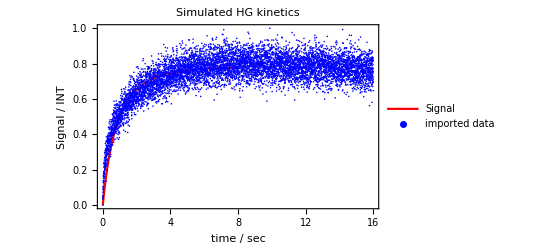
-Graphics-Initialize
Save Parameters

Exact input parameters  | Value | Error | Unit | Fixation
  K_equ(HD) =  |  |  | M^-1 |  | Fixed   | not fixed
affinity of guest for host |  |  |  | 
  k_1(HD) =  |  |  | M^-1s^-1 |  | Fixed   | not fixed
ingression rate constant |  |  |  | 
  k_-1(HD) =  |  |  | s^-1 | 
UnderBar[egression rate constant] |  |  |  | 
  Signal-0 =  |  |  | a.u. |  | Fixed   | not fixed
  Startsignal |  |  |  | 
  Signal-HD =  |  |  | a.u. |  | Fixed   | not fixed
  Signal from HD complex |  |  |  | 
  Signal-D =  |  |  | a.u. |  | Fixed   | not fixed
  Signal from dye alone |  | Click here to fit |  | Please keep in mind, that in this fitting model, all concentrations should be known and fixed. The affinity constants should be known as well as the ingression rate of the dye.

```mathematica
step = end/100.;




(*Import*)
	dataimport=Import[f,"Table"]; 
	end =  Max[dataimport[[All,1]]];
	step = end/100.;

If[jascoImport, 
i=1;
		dataHeader={};
		While[Not[NumericQ[dataimport[[i,1]]]],dataHeader=AppendTo[dataHeader,dataimport[[i,All]]];
i++;Off[Part::partw]];
		dataXY={};
While[NumericQ[dataimport[[i,1]]],dataXY=AppendTo[dataXY,dataimport[[i,All]]];i++;Off[Part::partw]];
		dataFooter={};While[i≤ First[Dimensions[dataimport]],dataFooter=AppendTo[dataFooter,dataimport[[i,All]]];i++];
		,
		dataXY=dataimport;
	];

If[resetToMin, 
	posMin=First[Flatten[Position[dataXY[[All,2]],Min[dataXY[[All,2]]]]]];
minimizedPart=Length[dataXY]-posMin+1;
	dataXY=Take[dataXY,-minimizedPart];

		,
		dataXY=dataXY;
	];
	
	ymax=Max[dataXY[[All,2]]];
	ymin=Min[dataXY[[All,2]]];
	adjusteddata=dataXY/.{x_,y_}-> {cfac*x/factor,normalize[y,ymax,ymin,normchoice]};
	
	end=Max[adjusteddata[[All,1]]];


(*Data summary*)

dataplot=Manipulate[
			Show[	
				
				ListPlot[{a2*adjusteddata},PlotStyle-> Blue,PlotRange->All],
				Plot[{a1*kinHDParaCacheSignalall[h0in,d0in,sig0in,sighdin,sigdin,tmin,tmax][khd1in,khd2in,sig0in,sighdin,sigdin][t]},{t,tmin,tmax},PlotStyle-> Red,PlotRange->All],
				PlotRange->All,PlotLegends->{"Signal","[HD_2]","[D]","[HG_A]","[G_A]","[H]"},ImageSize-> Large,AxesOrigin->{0,0},PlotLabel-> Style["Simulated Data","Subsection"],Frame->{{True,False},{True,False}},FrameLabel->{{"Signal / INT",None},{"time / sec",None}},FrameTicks->All
				],
			{{a1,1,Style["Signal",Red]},{1,0}},{{a2,1,Style["Data",Blue]},{1,0}},ControlPlacement->Right
			];

	
	
inputline2 = {
   {"Exact input parameters ", "Value", "Error","Unit", "Fixation"},
   
       
    
   
   (*Dye*)
 {Style["  K_equ(HD) = " , Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[kequhdin], FieldSize -> 8],InputField[Dynamic[kequhderror,None], FieldSize -> 8,Background->LightGray],  "M^-1",
    RadioButtonBar[Dynamic[kequhdfixed], {1 -> "Fixed", 2 -> "not fixed"}]},
   {"affinity of guest for host"},
      {Style["  k_1(HD) = " , Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[khd1in], FieldSize -> 8],InputField[Dynamic[khd1error,None], FieldSize -> 8,Background->LightGray],  "M^-1s^-1",
    RadioButtonBar[Dynamic[khd1fixed], {1 -> "Fixed", 2 -> "not fixed"}]},
{"ingression rate constant"}, {Style["  k_-1(HD) = " , Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[khd2in=khd1in/kequhdin,None], FieldSize -> 8,Background->LightGray], InputField[Dynamic[khga2error,None], FieldSize -> 8,Background->LightGray], "s^-1",
    ""},
   {"UnderBar[egression rate constant]"}, 
   
           
   
   
   (*Signals*)
   
   {Style["  Signal-0 = ", Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[sig0in], FieldSize -> 8],InputField[Dynamic[sig0error,None], FieldSize -> 8,Background->LightGray], "a.u.",
    RadioButtonBar[Dynamic[sig0fixed], {1 -> "Fixed", 2 -> "not fixed"}]},
{"  Startsignal"},
{Style["  Signal-HD = ", Bold, FontSize->16 ,TextAlignment->Right], InputField[Dynamic[sighdin], FieldSize -> 8],    InputField[Dynamic[sighderror,None], FieldSize -> 8,Background->LightGray],  "a.u.",
    RadioButtonBar[ Dynamic[sighdfixed], {1 -> "Fixed", 2 -> "not fixed"}]},
{"  Signal from HD complex"},{Style["  Signal-D = ", Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[sigdin], FieldSize -> 8], InputField[Dynamic[sigderror,None], FieldSize -> 8,Background->LightGray], "a.u.",
    RadioButtonBar[Dynamic[sigdfixed], {1 -> "Fixed", 2 -> "not fixed"}]},   
{"  Signal from dye alone","",{fitbutton}} 
};


	
	
	

Print[

kinShow[khd2in,khd1in,h0in,d0in,sig0in,sighdin,sigdin,tmin,tmax,species],
TableForm[{initializebutton,variablessavebutton}]]
Print[
Style[TableForm[inputline2, TableAlignments -> Left],"Subsubsection",Black,FontSize->18],
Style["Please keep in mind, that in this fitting model, all concentrations should be known and fixed. The affinity constants should be known as well as the ingression rate of the dye.",Bold]
]
```

```mathematica
Off[ParametricNDSolveValue::ivres];
inputparameter={};
subparameter={};
concparameter={};
output={};

(*Dye affinity parameters*)
Clear[h0];
Clear[d0];
If[d0fixed== 2,
	operator=1;
	
	AppendTo[inputparameter,{d0,d0in}], (*else*)
	d0=d0in;
	AppendTo[subparameter,{d0 -> d0in}];
];


(*Dye affinity parameters*)
Clear[khd1];
If[khd1fixed== 2,
	operator=1;
	
	AppendTo[inputparameter,{khd1,khd1in}], (*else*)
	khd1=khd1in;
	AppendTo[subparameter,{khd1 -> khd1in}];
];

Clear[khd2];
If[khd2fixed== 2,
	operator=1;
	
	AppendTo[inputparameter,{khd2,khd2in}], (*else*)
	khd2=khd2in;
	AppendTo[subparameter,{khd2 -> khd2in}];
];

Clear[kequhd];
If[kequhdfixed== 2,
	operator=1;
	
	AppendTo[inputparameter,{kequhd,kequhdin}], (*else*)
	kequhd=kequhdin;
	AppendTo[subparameter,{kequhd -> kequhdin}];
];
		
	Clear[sighd];
If[sighdfixed==2,
operator=1;
AppendTo[inputparameter,{sighd,sighdin}], (*else*)
sighd=sighdin;
AppendTo[subparameter,{sighd -> sighdin}];
];
	Clear[sigd];
If[sigdfixed== 2,
operator=1;
AppendTo[inputparameter,{sigd,sigdin}], (*else*)
sigd=sigdin;
AppendTo[subparameter,{sigd -> sigdin}];
];
	Clear[sig0];
If[sig0fixed== 2,
operator=1;
AppendTo[inputparameter,{sig0,sig0in}], (*else*)
sig0=sig0in;
AppendTo[subparameter,{sig0 -> sig0in}];
];
```

```mathematica
fitsignal2=NonlinearModelFit[adjusteddata,kinHDParaCacheSignalall[h0in,d0in,sig0in,sighdin,sigdin,tmin,tmax][khd1,khd2,sig0,sighd,sigd][t],inputparameter,t];
ClearAll[h0,d0,sig0,sighd,sigd,khd1,kequhd]

	bestfit=TableForm[fitsignal2["ParameterTableEntries"]];
	(*signal results*)

	sig0out=sig0/.fitsignal2["BestFitParameters"];
	sig0pos=Flatten[Position[bestfit[[1,All,1]],sig0out]];
If[NumericQ[sig0out],
	sig0error=First[bestfit[[1,sig0pos,2]]];
	sig0in=sig0out;
];

	sighdout=sighd/.fitsignal2["BestFitParameters"];
	sighdpos=Flatten[Position[bestfit[[1,All,1]],sighdout]];
If[NumericQ[sighdout],
	
	sighderror=First[bestfit[[1,sighdpos,2]]];
	sighdin=sighdout;
];

		sigdout=sigd/.fitsignal2["BestFitParameters"];
		sigdpos=Flatten[Position[bestfit[[1,All,1]],sigdout]];
	If[NumericQ[sigdout],
	
	sigderror=First[bestfit[[1,sigdpos,2]]];
	sigdin=sigdout;
];

(*affinity results*)

	khd1out=khd1/.fitsignal2["BestFitParameters"];
	khd1pos=Flatten[Position[bestfit[[1,All,1]],khd1out]];
	If[NumericQ[khd1out],
	
	khd1error=First[bestfit[[1,khd1pos,2]]];
	khd1in=khd1out;
];



	kequhdout=kequhd/.fitsignal2["BestFitParameters"];
	kequhdpos=Flatten[Position[bestfit[[1,All,1]],kequhdout]];
	If[NumericQ[kequhdout],
	
	kequhderror=First[bestfit[[1,kequhdpos,2]]];
	kequhdin=kequhdout;
];

	

(*accumulate data for export file*)
	


(*accumulate data for export file*)


fitplot=Manipulate[
			Show[	
				ListPlot[{a2*adjusteddata},PlotStyle-> Blue,PlotRange->All],
				Plot[{a1*kinHDParaCacheSignalall[kequhdin,khd1in,h0in,d0in,sig0in,sighdin,sigdin,tmin,tmax][khd1in,kequhdin,sig0in,sighdin,sigdin][t]},{t,tmin,tmax},PlotStyle-> Red,PlotRange->All],
				PlotRange->All,PlotLegends->{"Fitted Signal","[HD_2]","[D]","[HG_A]","[G_A]","[H]"},ImageSize-> Large,AxesOrigin->{0,0},GridLines->{{},{}},PlotLabel-> Style["Fitted Data","Subsection"]
				],
			{{a1,1,Style["Fitted Signal",Red]},{1,0}},{{a2,1,Style["Data",Blue]},{1,0}},ControlPlacement->Right
			];


exportbutton=MouseAppearance[Button[stylesButtonGenericStyle["Save Fitting","Save the simulated data as comma delimited .csv"],
Export[SystemDialogInput["FileSave",".csv"],output],Method->"Queued",Appearance->None

],"LinkHand"];

datageneratebutton=MouseAppearance[Button[stylesButtonGenericStyle["Generate saveable Data","Generate Datapoints for CSV export"],
output=kinGenerateOutput[kequhdin,khd1in,h0in,d0in,sig0in,sighdin,sigdin,tmin,tmax,N[200]];
outputinfo=Style[TableForm[output[[1;;12,5;;7]]],"Menu"]
,Appearance->None

],"LinkHand"];

Print[fitplot,TableForm[{"","",{datageneratebutton},"", Dynamic[outputinfo],"",exportbutton}]]
(*put1=Prepend[Prepend[fitteddata,units],header1];
put2=Prepend[Prepend[adjusteddata,units],header2];
output=Join[put1,List/@put2[[All,1]],List/@put2[[All,2]],List/@column1,List/@column2,List/@column3,2];

exportbutton1=MouseAppearance[Button[stylesButtonGenericStyle["Save","Save the fitted and acquired data"],Export[SystemDialogInput["FileSave",".csv"],output],Method->"Queued",Appearance->None],"LinkHand"];
halflifebutton=MouseAppearance[Button[stylesButtonGenericStyle["Calculate Half-Life","Calculate the half-life of the reaction"],
hl=signalmodeldata[[Flatten[Position[signalmodeldata[[All,2]],SelectFirst[signalmodeldata[[All,2]],Round[#,0.001]== Round[2*Min[signalmodeldata[[All,2]]],0.001]&]]],All]],Appearance->None],"LinkHand"];
Print[
fitplot,
Style[TableForm[inputs],"Section",Black,FontSize->18],"  ",
TableForm[{{"  You can save fitted data:",exportbutton1}}]
];
Print[

TableForm[{{"half-life:", Dynamic[Flatten[hl][[1]]],"sec"},halflifebutton}]
];*)
```

InterpolatingFunction::dmval: Input value {8.002} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {8.004} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {8.006} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.